# 0. Initial data

## 0.1 Dataset

```mathematica
width = 0.003;(*мм*)
q = 10^-6;(*м^2/с*)
λ =10;(*Вт/(м*C)*)
τ1 = 50;(*C*)
τ2 = 20;(*C*)
α1 = 30;(*Вт/(м^2 К)*)
α2 = 10;(*Вт/(м^2 К)*)
n = 10;
t0=20;
dx = width / (n - 1)
plotRange = {{1, n}, {20, 50}};
markers = Graphics[Circle[],ImageSize->10];
```

0.000333333

# 1. Решение одномерных задач

## 1.1 Стационарная одномерная задача

#### 1.1.1 Стационарная одномерная задача

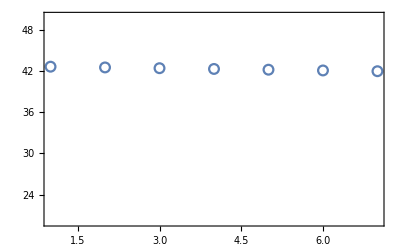

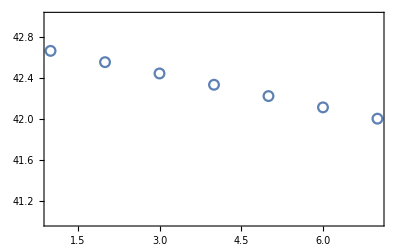

```mathematica
temperatures = Table[Symbol["$t"<>ToString@i],{i,n}];
(*equations*)
FormInnerEq[i_] := Function[(temperatures[[i + 1]] - 2* temperatures[[i]] + temperatures[[i-1]])/dx^2 == 0][{temperatures[[i + 1]],temperatures[[i]],temperatures[[i-1]]}]
FormEdgeEq1 := Function[(temperatures[[2]]-temperatures[[1]])/dx+ α1*(τ1-temperatures[[1]])==0][{temperatures[[2]],temperatures[[1]]}]
FormEdgeEq2 := Function[-(temperatures[[n]]-temperatures[[n-1]])/dx+ α2*(τ2-temperatures[[n]])==0][{temperatures[[n]],temperatures[[n-1]]}]

(*creating system of equations*)
equations = {};
AppendTo[equations, FormEdgeEq1];
For[i = 2, i ≤ n - 1, i++, AppendTo[equations, FormInnerEq[i]]];
AppendTo[equations, FormEdgeEq2];
result = temperatures /. Solve[equations, temperatures];
result;
ListPlot[result, PlotRange->plotRange, PlotMarkers->markers, Frame->True]
ListPlot[result,PlotRange->{{1,n},{41, 43}},PlotMarkers->markers, Frame->True]
```

## 1.2 Interpolation polynomial

```mathematica
CalcTau:= Module[{t=dx^2/(2q),n=0},
While[t<1, t=t*10;n++];
Return[dx^2/(2q)-(t*10^n-Floor[t*10^n])/10^n]]
dt = CalcTau
nt = 10;
```

0.05

#### Common

```mathematica
(*matrix of variables*)
FormVars[m_, n_]:=Return[Table[Symbol["$t"<>ToString@i<>"x"<>ToString@j],{i,m}, {j, n}]];

(*creates equation for init moment of time*)
FormInitTime[matr_,i_] := Function[matr[[i]][[1]]==t0][matr[[i]][[1]]]

(*creats border conditions equations*)
FormEdgeEq1NonStat[matr_,j_,a_,b_] := Function[(matr[[b]][[j]]-matr[[a]][[j]])/dx+ α1*(τ1-matr[[a]][[j]])==0][{matr[[b]][[j]],matr[[a]][[j]]}];
FormEdgeEq2NonStat[matr_,j_,a_,b_] := Function[-(matr[[b]][[j]]-matr[[a]][[j]])/dx+ α2*(τ2-matr[[b]][[j]])==0][{matr[[b]][[j]],matr[[a]][[j]]}];

(*combines all equations*)
createEquationsNonStat[vars_,pts0_, tms0_, isExplicit_]:=Module[{i=0,j=0, equations ={}, pts=pts0, tms=tms0,t=vars},
(*adds border conditions for the 1st and the last point*)
For[j=1,j≤tms,j++,
AppendTo[equations, FormEdgeEq1NonStat[t,j,1,2]];
AppendTo[equations, FormEdgeEq2NonStat[t,j,pts-1,pts]]];

(*adds equations for inner points*)
For[i=2,i<pts,i++,For[j=1,j<tms,j++,
(*adds equations for initial time*)
If[j==1,AppendTo[equations,FormInitTime[t,i]]];
(*adds equations for all time moments, except initial*)
If[¬isExplicit,
AppendTo[equations,FormInnerEqImplicit[t,i,j]],
AppendTo[equations,FormInnerEqExplicit[t,i,j+1]]]];
];
Return[equations]];

(*calculates temperatures*)
temps[pts0_, tms0_, isExplicit_] := Module[{i=1, j=1, temp={}, result = {},pts=pts0, tms=tms0,t=FormVars[pts0,tms0]},
For[i=1,i≤pts,i++,For[j=1,j≤tms,j++,AppendTo[temp, t[[i]][[j]]]]];
result = temp /.Solve[createEquationsNonStat[t,pts,tms,isExplicit], temp][[1]];
Return[ArrayReshape[result, {pts, tms}]]
]
```

#### Explicit

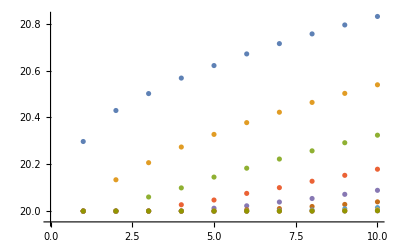

```mathematica
FormInnerEqExplicit[matr_,i_,j_] := Function[(matr[[i]][[j]] - matr[[i]][[j-1]])/dt == q(matr[[i+1]][[j-1]]-2matr[[i]][[j-1]]+matr[[i-1]][[j-1]])/dx^2][{matr[[i-1]][[j-1]],matr[[i]][[j-1]],matr[[i+1]][[j-1]],matr[[i]][[j]]}];

ListPlot[temps[n,nt, True]]
```

#### Implicit

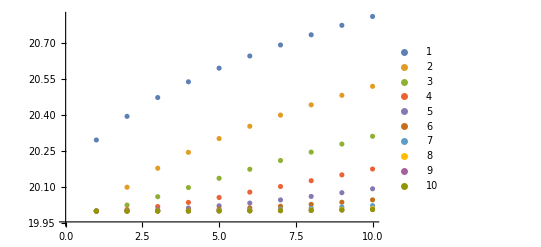

```mathematica
FormInnerEqImplicit[matr_,i_,j_] := Function[(matr[[i]][[j+1]] - matr[[i]][[j]])/dt == q(matr[[i+1]][[j+1]]-2matr[[i]][[j+1]]+matr[[i-1]][[j+1]])/dx^2][{matr[[i-1]][[j+1]],matr[[i]][[j+1]],matr[[i+1]][[j+1]],matr[[i]][[j]]}];

ListPlot[temps[n,nt, False], PlotLegends->Automatic]
```